```mathematica
(*sbc fit*)
(*(1-d)-(a^2*Sin[π*c*Sqrt[(x-b)^2+a^2]]^2)/((x-b)^2+a^2)*)
```

## Values

```mathematica
ftwToFrequencyMHz=(1.*^-6)*(1.*^9)/(Interpreter["HexInteger"]["FFFFFFFF"]);
mhz=1.*^6;
khz=1.*^3;
```

## Plotting

```mathematica
(*set plot options*)
SetOptions[Plot,Frame-> True,FrameTicksStyle-> Directive[Black,15],Background->White,ImageSize->Large,GridLines->Automatic];
SetOptions[ListPlot,Frame-> True,FrameTicksStyle-> Directive[Black,15],Joined->False,Background->White,ImageSize->Large,GridLines->Automatic];
SetOptions[ListLinePlot,Frame-> True, FrameTicksStyle-> Directive[Black,15],Background->White,ImageSize->Large,GridLines->Automatic,GridLines->Automatic];
SetOptions[ListLogPlot,Frame-> True, FrameTicksStyle-> Directive[Black,15],Joined->True,Background->White,ImageSize->Large,GridLines->Automatic];SetOptions[ListLogLogPlot,Frame-> True, FrameTicksStyle-> Directive[Black,15],Joined->True,Background->White,ImageSize->Large,GridLines->Automatic];
SetOptions[Histogram,Frame-> True, FrameTicksStyle-> Directive[Black,15],Background->White,ImageSize->Large,GridLines->Automatic];
SetOptions[ComplexListPlot,Frame-> True,FrameTicksStyle-> Directive[Black,15],Background->White,ImageSize->Large,GridLines->Automatic];
```

```mathematica
(*set signal plot options*)
SetOptions[Histogram,Frame-> True, FrameTicksStyle-> Directive[Black,15],Background->White,ImageSize->Large,GridLines->Automatic];
SetOptions[ComplexListPlot,Frame-> True,FrameTicksStyle-> Directive[Black,15],Background->White,ImageSize->Large,GridLines->Automatic];
```

```mathematica
(*set 3d plot options*)
SetOptions[ListDensityPlot,Frame-> True, FrameTicksStyle-> Directive[Black,15],Background->White,ImageSize->Large,GridLines->Automatic];
SetOptions[ListPlot3D,Background->None,ImageSize->Large];
```

## Import

```mathematica
(*datasetName="C:\\Users\\EGGS2\\Documents\\tmp1\\000025003-QLMSRabi.h5";*)
datasetName="C:\\Users\\EGGS2\\Documents\\tmp1\\000025004-QLMSRamsey.h5";
```

### Import

```mathematica
(*import dataset*)
res00=Import[datasetName,{"/datasets/results"}];
```

## Process

### Convert

```mathematica
(*rearrange for columns: secular (kHz), readout, carrier, counts*)
res01=Transpose[{
res00[[;;,1]]*ftwToFrequencyMHz,(*readout/AOM, MHz*)
res00[[;;,3]]*ftwToFrequencyMHz*(1.*^3),(*tickle, kHz*)
res00[[;;,2]](*counts*)
}];
(*sample data*)
res01[[1]]
```

{102.852,1099.25,121.}

```mathematica
(*guess carrier frequency*)
carrierFreqMHz=Mean[res01[[;;,1]]];
(*find count threshold*)
countThreshold=FindThreshold[res01[[;;,-1]]];
```

```mathematica
(*create copy of dataset and directly threshold counts into states*)
res10=res01;
res10[[;;,-1]]=UnitStep[res01[[;;,-1]]-countThreshold];
(*average states into probabilities*)
res11=GroupBy[
res10,
#[[;;2]]&,
N[Mean[#]]&
]//Values;
```

### Rearrange

```mathematica
(*separate into rsb and bsb*)
(*final output: {bsb/rsb, readout/AOM freq (MHz), secular freq (kHz), probability}*)
res20=GatherBy[
res11,
First[#]<carrierFreqMHz&
];
(*sort frequencies by order*)
res20=Map[
SortBy[#,First]&,
res20,
{1}
];
(*sample dimensions*)
res20//Dimensions
res20[[1,1]]
```

{2,697,3}

{102.85,1099.,0.9}

### Plot

```mathematica
resPlots={
ListDensityPlot[
res20[[2]],
PlotRange->Full,
PlotLegends->Automatic,
ColorFunctionScaling->False,
FrameLabel->{ 
{Style["Tickle Frequency (kHz)",{Black,Directive[15]}],None},
{Style["Readout Frequency (MHz)",{Black,Directive[15]}],
Style["QLMS - RSB",{Black,Directive[15]}]}
},
ImageSize->Large
],
ListDensityPlot[
res20[[1]],
PlotRange->Full,
PlotLegends->Automatic,
ColorFunctionScaling->False,
FrameLabel->{ 
{Style["Tickle Frequency (kHz)",{Black,Directive[15]}],None},
{Style["Readout Frequency (MHz)",{Black,Directive[15]}],
Style["QLMS - BSB",{Black,Directive[15]}]}
},
ImageSize->Large
]
};
```

## Show

### Single Point

```mathematica
(*ListPlot[
#,
Joined->False,
PlotRange->{0,1}
]&/@res21[[1,;;,;;,{1,3}]]*)
```

### Full Scan

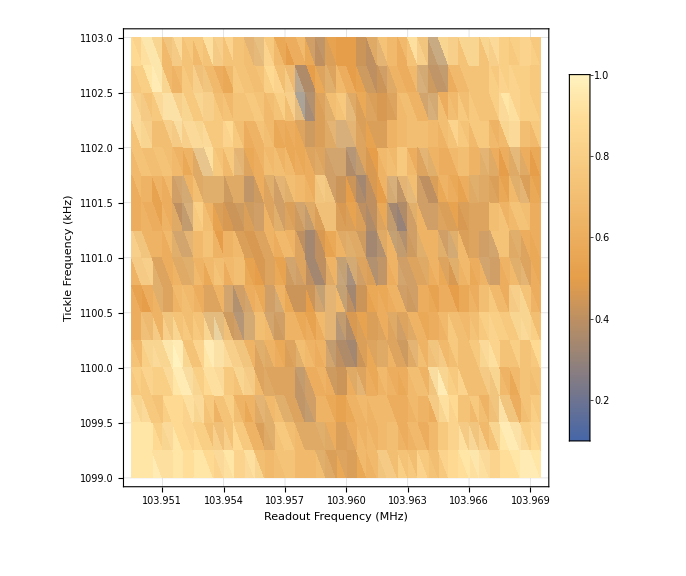
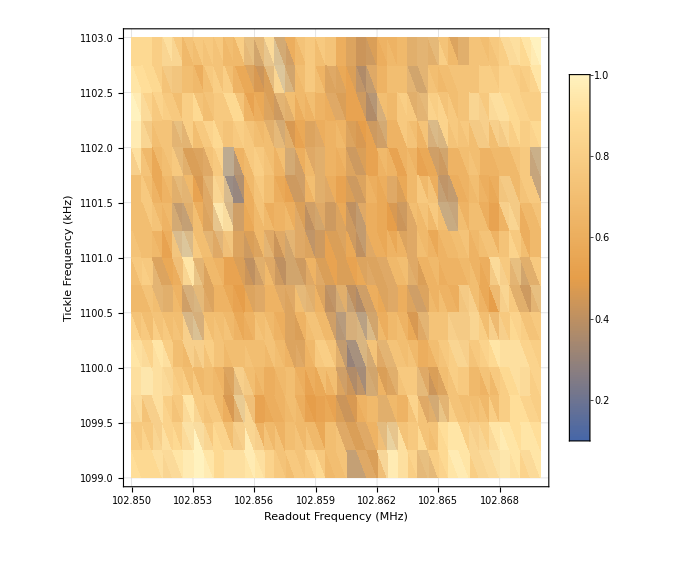

```mathematica
resPlots
```

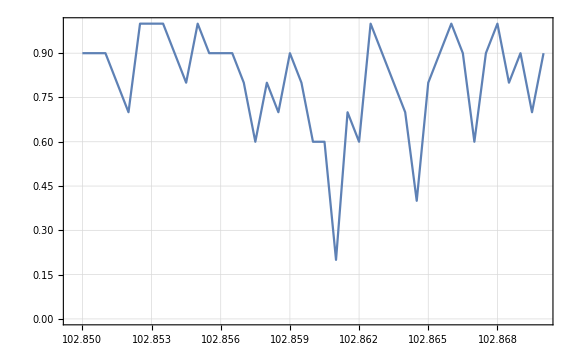
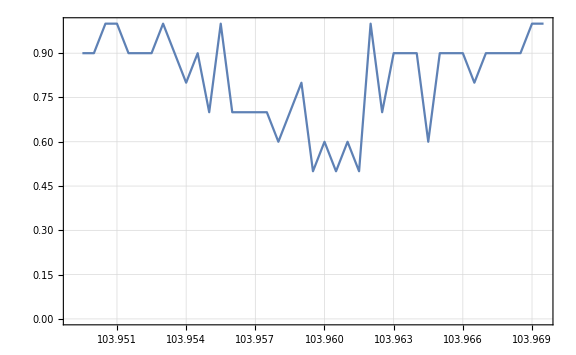
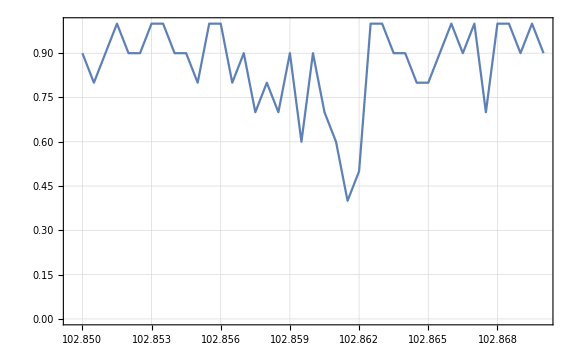
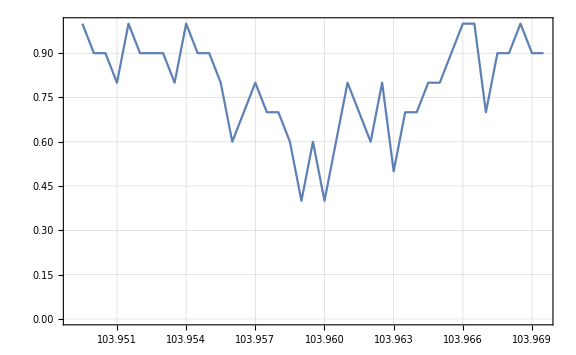
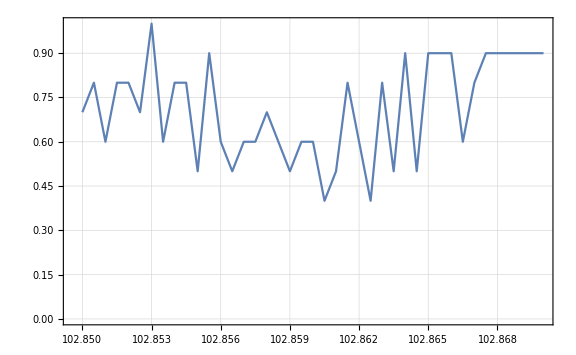
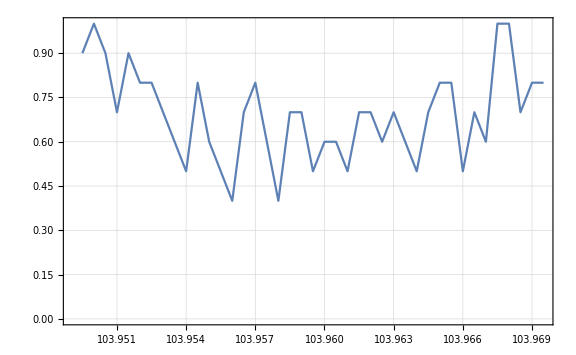
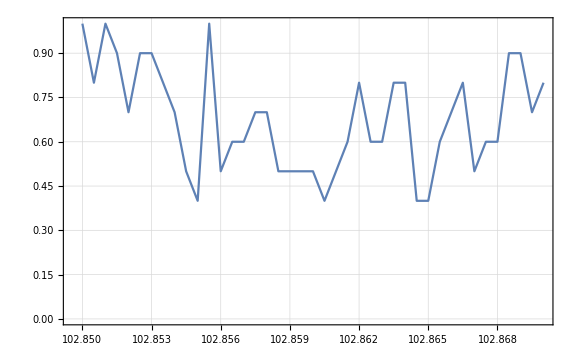
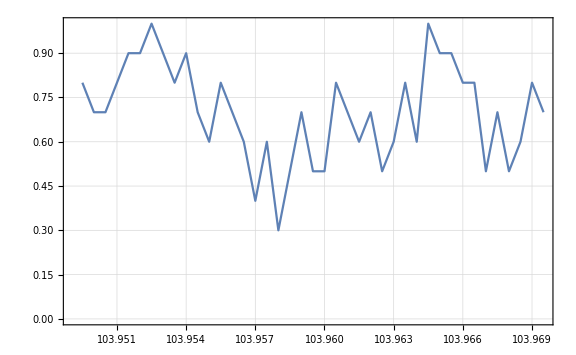

```mathematica
(*individual plots*)
th0=GroupBy[
#,
#[[2]]&,
#[[;;,{1,3}]]&
]&/@res20;
{
ListPlot[th0[[1,#]],Joined->True],
ListPlot[th0[[2,#]],Joined->True]
}&/@Range[Length[th0[[1]]]]
```